```mathematica
r= {0.4,0.1};
b={{0.05,0.1},{0.08,0.003}};
dx1[x1_,x2_]:=r[[1]] * x1 -b[[1,1]]*(x1)^2-b[[1,2]]*x1*x2;
dx2[x1_,x2_]:=-r[[2]] * x2 -b[[2,2]]*(x2)^2+b[[2,1]]*x1*x2;
cond1 = {x1[0]==1.0,x2[0]==4.0};
cond2 ={x1[0]==2,x2[0]==2}; 
cond3 ={x1[0]==1,x2[0]==1}; 
cond4 = {x1[0]==1,x2[0]==1,x3[0]==1};
T01 = 0; TN1 = 150;
T02= 0; TN2 = 0.2;
T03= 0; TN3 = 0.1;
T04= 0; TN4 = 0.1;

NP = 1000;
res1=NDSolve[{x1'[t]==r[[1]] * x1[t] -b[[1,1]]*(x1[t])^2-b[[1,2]]*x1[t]*x2[t], x2'[t]==-r[[2]] * x2[t] -b[[2,2]]*(x2[t])^2+b[[2,1]]*x1[t]*x2[t],cond1},{x1,x2},{t,T01,TN1}];
res2 = NDSolve[{x1'[t]==2 * x1[t] +(x2[t])^2-1, x2'[t]==6*x1[t] -(x2[t])^2+1,cond2},{x1,x2},{t,T02,TN2}];
res3 = NDSolve[{x1'[t]==1 -(x2[t])^2-(x1[t])^2, x2'[t]==2*x1[t] ,cond3},{x1,x2},{t,T03,TN3}];
res4 = NDSolve[{x1'[t]==10(x2[t]-x1[t]), x2'[t]==x1[t]*(28 - x3[t])-x2[t] ,x3'[t]==x1[t]*x2[t]-8/3*x3[t],cond4},{x1,x2,x3},{t,T04,TN4}];
```

```mathematica
SetDirectory[NotebookDirectory[]] 
data1 = Import["ExplicitEuler.dat"];
data2 = Import["ImplicitEuler.dat"];
data3= Import["Symmetrical.dat"];
data4 = Import["Runge_Kutta_2.dat"];
data5= Import["Runge_Kutta_4.dat"];
data6= Import["Adams_Bashforth.dat"];
data7= Import["Forecast_correction.dat"];
data8= Import["Runge_Kutta_4_adaptive.dat"];
(*ExplicitEuler,ImplicitEuler,Symmetrical,Runge_Kutta_4,Adams_Bashforth,*)
```

/Users/arsenytokarev/Desktop/BMSTU_coopmode_labs/Numerical_methods_6/Lab1/output

```mathematica
data = data8;
res = res3;
T0=T03;
TN=TN3;
```

```mathematica
(*,PlotRange->{{0.5,2},{2.5,4}}*)
```

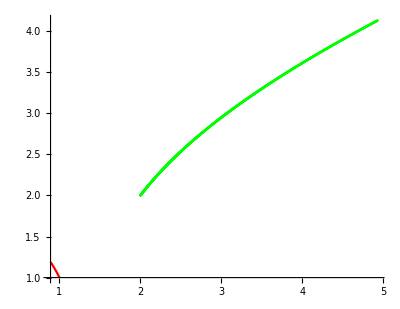

```mathematica
Show[ParametricPlot[Evaluate[{x1[t],x2[t]}/.res],{t,T0,TN},PlotStyle->Red,PlotRange->All],ListPlot[data,PlotStyle->Green]]
```

```mathematica
dataT1=Table[{T0+(i-1)/(NP-2)*TN,data[[i,1]]},{i,1,NP-1}];
dataT2=Table[{T0+(i-1)/(NP-2)*TN,data[[i,2]]},{i,1,NP-1}];
```

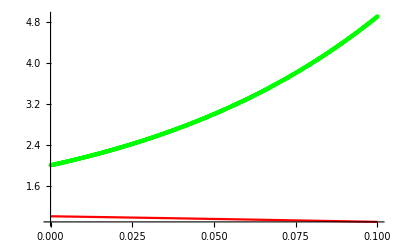

```mathematica
Show[Plot[Evaluate[x1[t]/.res],{t,T0,TN},PlotRange->All,PlotStyle->Red],ListPlot[dataT1,PlotStyle->Green]]
```

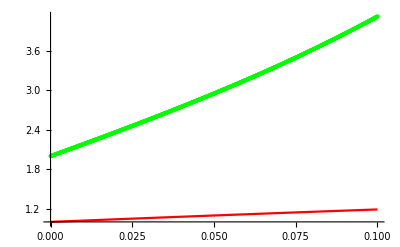

```mathematica
Show[Plot[Evaluate[x2[t]/.res],{t,T0,TN},PlotRange->All,PlotStyle->Red],ListPlot[dataT2,PlotStyle->Green]]
```

```mathematica
Show[ParametricPlot3D[Evaluate[{x1[t],x2[t],x3[t]}/.res4],{t,T04,TN4},PlotStyle->Red,PlotRange->All],ListPointPlot3D[data,PlotStyle->Green]]
```

-Graphics3D-

```mathematica
norms = Import["Runge_Kutta_4_norms.dat"];
steps = Import["Runge_Kutta_4_steps.dat"];
```

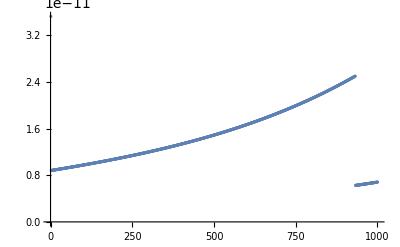

```mathematica
ListPlot[norms]
```

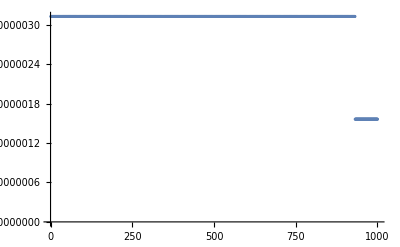

```mathematica
ListPlot[steps]
```

```mathematica
phase1= Table[Import[StringJoin["phaseExplicitEuler/r=", StringJoin[ToString[i], ".dat"]]], {i, -20, 20}];
phase2= Table[Import[StringJoin["phaseImplicitEuler/r=", StringJoin[ToString[i], ".dat"]]], {i, 0, 239}];
phase3= Table[Import[StringJoin["phaseSymmetrical/r=", StringJoin[ToString[i], ".dat"]]], {i, -20, 20}];
phase4= Table[Import[StringJoin["phaseRK2/r=", StringJoin[ToString[i], ".dat"]]], {i, -20, 20}];
phase5= Table[Import[StringJoin["phaseRK4/r=", StringJoin[ToString[i], ".dat"]]], {i, -20, 20}];
(*phase6= Table[Import[StringJoin["phaseRK4_adaptive/r=", StringJoin[ToString[i], ".dat"]]], {i, -20, 20}];*)
phase7= Table[Import[StringJoin["phaseAB/r=", StringJoin[ToString[i], ".dat"]]], {i, -20, 20}];
phase8= Table[Import[StringJoin["phaseFC/r=", StringJoin[ToString[i], ".dat"]]], {i, -20, 20}];
phase = phase2;
```

```mathematica
ListPlot[phase]
```

-Graphics-